# Versuch 41

```mathematica
ClearAll["Global`*"]
```

## Import Data

```mathematica
files=FileNames["*.csv",NotebookDirectory[],2];
```

```mathematica
numbers=ToExpression[StringTake[StringSplit[StringSplit[#1,"\\"]⟦-1⟧,"CH"]⟦1⟧,2;;-1]]&/@files;
```

## First Channel

```mathematica
data1=Import/@files[[1;;8]];
```

```mathematica
dataProcessed1=#[[All,{4,5}]]&/@data1;
```

```mathematica
plts=Table[ListLinePlot[dataProcessed[[i]],PlotRange->All,PlotLabel->ToString[i-1]],{i,1,Length[dataProcessed]}];
```

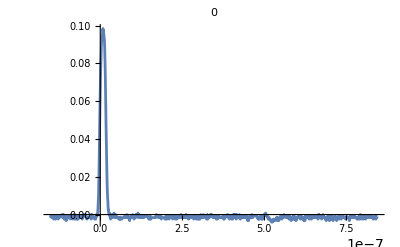

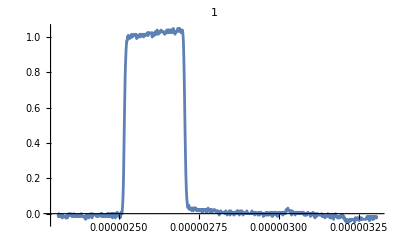

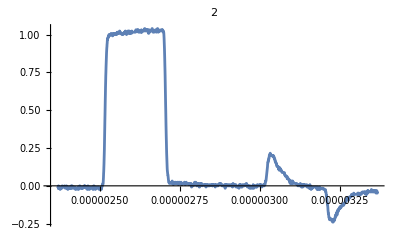

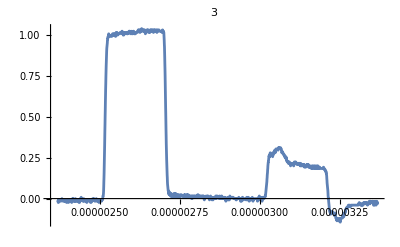

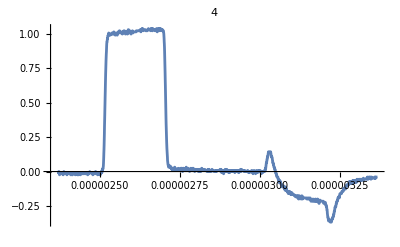

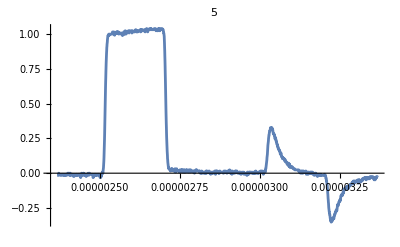

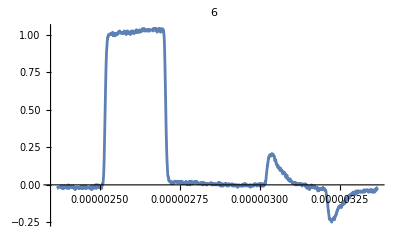

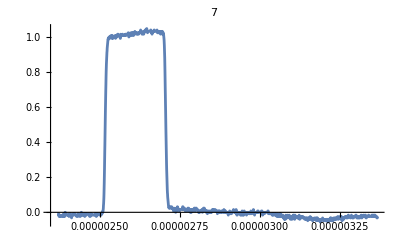

{Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Print/@plts
```

## Multi Channel Plots

```mathematica
indices2=Range[11,16]
```

{11,12,13,14,15,16}

```mathematica
Length[files]
```

9

```mathematica
data2=Import/@files[[indices2]]
```